```mathematica
DSolve[y'[t]==3*y[t]+3*t,y,{t,0,2}]
```

DSolve::dvnoarg: The function y' appears with no arguments.

DSolve[y'==3 t+3 y,y,{t,0,2}]

```mathematica
Plot[DSolve[y'[t]==3*y[t]+3*t,y,{t,0,2}],{t,0,2}]
```

DSolve::derlen: The length of the derivative operator Derivative[1] in SuperscriptBox[ is not the same as the number of arguments.

NDSolve::dsvar: 0.0000408571 cannot be used as a variable.

DSolve::derlen: The length of the derivative operator Derivative[1] in SuperscriptBox[ is not the same as the number of arguments.

NDSolve::dsvar: 0.0408572 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

DSolve::derlen: The length of the derivative operator Derivative[1] in SuperscriptBox[ is not the same as the number of arguments.

General::stop: Further output of DSolve :: derlen will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[y->Function[{t},-1/3-t+ⅇ^(3 t) C[1]],{t,0,2}]
```

-Graphics-

```mathematica
DSolve[y'[t]==3*y[t]+3*t,y,{t,0,2}]
```

{{y→Function[{t},-1/3-t+ⅇ^(3 t) C[1]]}}

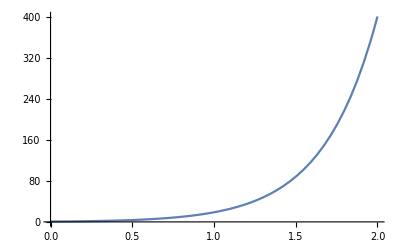

```mathematica
Plot[-1/3-t+Exp[3*t],{t,0,2},PlotLegends->"Expressions"]
```

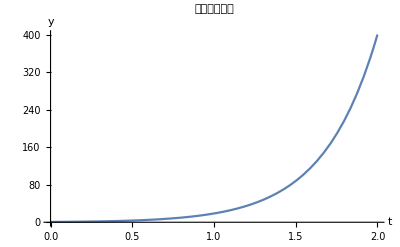

```mathematica
Show[%6,AxesLabel->{HoldForm[t],HoldForm[y]},PlotLabel->HoldForm[精确解的图像],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["E:\\MyMathMa\\figure1.png",%7,"PNG"]
```

E:\MyMathMa\figure1.png

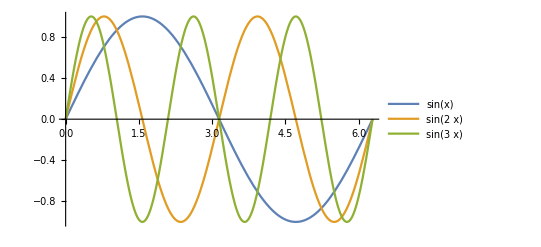

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

```mathematica
Plot[-1/3-t+Exp[3*t],{t,0,2},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
Plot[-1/3-t+Exp[3 t],{t,0,2},PlotTheme->Automatic,PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
Plot[{-1/3-t+Exp[3*t],{}},{t,0,2}]
```

-Graphics-